291

277.41+72.2338 x^0.105151

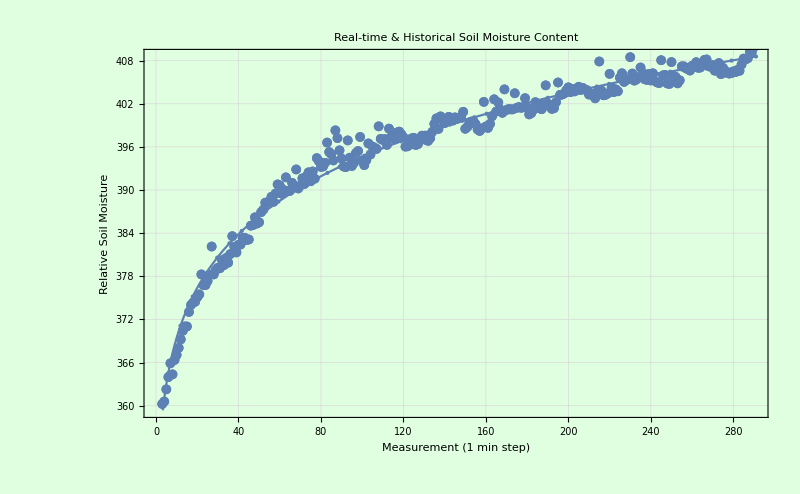

Export::nodir: Directory D:\Google Drive_Moist\ does not exist.

Export::noopen: Cannot open D:\Google Drive_Moist\SoilMoisturePlot.jpg.

```mathematica
MoistData = Import["D:\\Google Drive_Moist\\screenlog.0"] ;(* Imports data from updated google drive folder on desktop *) 
MoistData[[1]]; (* Test to see format of text file *)
Measurements=Dimensions[MoistData][[1]] (* Determination of the number of measurements and entries in screenlog file *)
MoistData[[1,3]];  (* Test of what position the soil moisture data is *)
nlm=NonlinearModelFit[Table[MoistData[[i,3]],{i,1,Measurements}],a+b*x^c,{a,b,c},x] ;(* Nonlinear fit of the data using a + bx^c as the fit model *)
DataFit=Normal[nlm] (* Normalizing the model output to use in the plot function *)
imageSize = 800; (* Constant for the size of generated plots *)
FittedData=Plot[DataFit,{x,0,Measurements},Frame->True,FrameLabel->{"Measurement (1 min step)","Relative Soil Moisture"},ImageSize->imageSize,Mesh->Full,FrameStyle->Black,BaseStyle->16,PlotLabel->Style["Real-time & Historical Soil Moisture Content",Black],GridLines->Automatic,Background->LightGreen]; (* Independent graph for the model *)

DataListPlot=ListPlot[Table[MoistData[[i,3]],{i,1,Measurements}],Frame->True,FrameLabel->{"Measurement (1 min step)","Relative Soil Moisture"},ImageSize->imageSize,Mesh->Full,Joined->False,FrameStyle->Black,BaseStyle->16,PlotLabel->Style["Real-time & Historical Soil Moisture Content",Black],GridLines->Automatic,Background->LightGreen,PlotMarkers->{Automatic,10}]; (* Independent graph for the raw data *)

SoilMoisturePlot=Show[{FittedData,DataListPlot}] (* Combined plot of the raw data and model *)

Export["D:\\Google Drive_Moist\\SoilMoisturePlot.jpg",SoilMoisturePlot]; (* Export of the combined graph to the google drive folder on the desktop, which is rewritten everytime this file is runned *)
```

Prediction for When SM Content Is Dry

```mathematica
DryTime=Solve[DataFit == 430,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1226.72}}

```mathematica
Print["Time until soil needs to be watered: ",N[DryTime[[1,1,2]]*1/60,2]," hours"]
```

Time until soil needs to be watered: 20.4454 hours